```mathematica
Clear["Global`*"]
```

```mathematica
inputData = Import[NotebookDirectory[]<>"/input.txt"];
input = StringSplit[inputData];
l=Length[input];(*l will have to be even*)
(*Write a function here that will take in strings as variable names*)
dt=Read[StringToStream[input[[2]]]];
tmax=input[[4]];
nTrajectory=input[[6]];
nstore=input[[8]];
yWall=input[[10]];
sigmaXX=input[[12]];
sigmaXZ=input[[14]];
transitTime=input[[16]];
sigmaPX=input[[18]];
sigmaPY=input[[20]];
sigmaPZ=input[[22]];
density=input[[24]];
rabi=input[[26]];
kappa=input[[28]];
name =input[[30]]
```

tau10_dens10_g2_k40

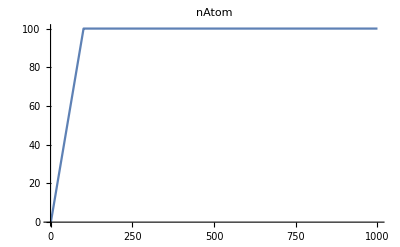

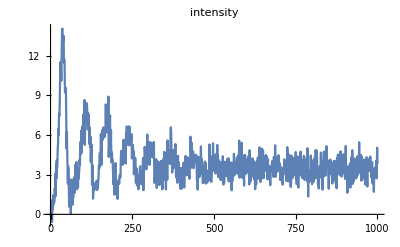

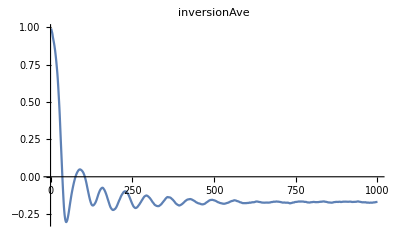

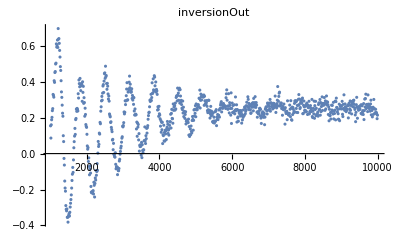

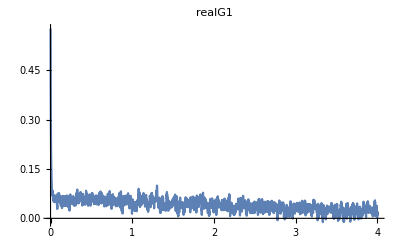

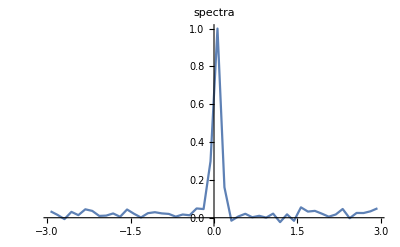

```mathematica
(*When doing one run*)
intensity=Flatten[Import[NotebookDirectory[]<>name<>"/intensity.dat"]];
nAtom=Flatten[Import[NotebookDirectory[]<>name<>"/nAtom.dat"]];
inversionAve=Flatten[Import[NotebookDirectory[]<>name<>"/inversionAve.dat"]];
szFinal=Flatten[Import[NotebookDirectory[]<>name<>"/szFinal.dat"]];
realG1 = Import[NotebookDirectory[]<>name<>"/realG1.dat"];
spectra=Import[NotebookDirectory[]<>name<>"/spectra.dat"];
ListLinePlot[nAtom,PlotRange->All,PlotLabel->"nAtom"]
ListLinePlot[intensity,PlotRange->All,PlotLabel->"intensity"]
ListLinePlot[inversionAve,PlotRange->All,PlotLabel->"inversionAve"]
ListPlot[szFinal,PlotRange->All,PlotLabel->"inversionOut"]
ListLinePlot[realG1,PlotRange->All,PlotLabel->"realG1"]
ListLinePlot[spectra,PlotRange->All,PlotLabel->"spectra"]
```

FittedModel[0.0145598/(0.0068026+4 x^2)]

| Estimate | Standard Error | t-Statistic | P-Value
linewidth | 0.0824779 | 0.0810415 | 1.01772 | 0.314132
A | 0.176529 | 0.0722132 | 2.44456 | 0.018394

0.0824779

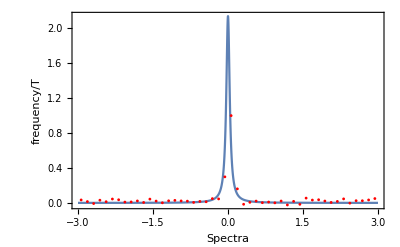

```mathematica
(*Fit the spectra to lorentzian*)
lorentzianModel=A linewidth/(linewidth^2+4x^2);
fitLoren=NonlinearModelFit[spectra,{lorentzianModel},{linewidth,A},{x}]
fitLoren["ParameterTable"]
linewidth1 = linewidth/.fitLoren["BestFitParameters"]
Show[{Plot[fitLoren[x],{x,-3,3},PlotRange->All,BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.005],Map[Point,spectra]}]},Frame->True,FrameLabel->{"Spectra","frequency/T"}]
```

```mathematica
tauc1=1/(linewidth1 Pi)
```

3.85934

B ⅇ^(-t/tc)

FittedModel[0.0691283 ⅇ^(-0.291114 t)]

| Estimate | Standard Error | t-Statistic | P-Value
tc | 3.43508 | 0.079546 | 43.1836 | 9.4092826146×10^-335
B | 0.0691283 | 0.000764334 | 90.4426 | 1.3143428831×10^-969

3.43508

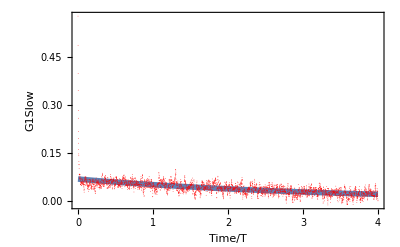

```mathematica
(*Fit the G1 function to exponential*)
exponentialModel=B Exp[- t/tc]
fitExp=NonlinearModelFit[realG1,{exponentialModel},{tc,B},{t}]
fitExp["ParameterTable"]
tauc2=tc/.fitExp["BestFitParameters"]
Show[{Plot[fitExp[x],{x,0,Last[realG1][[1]]},PlotRange->All,PlotStyle->{Thickness[0.01]},BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.001],Map[Point,realG1]}]},Frame->True,FrameLabel->{"Time/T","G1Slow"}]
```

```mathematica
(*Get the linewidth from the coherent time*)
linewidth2 = 1/(tauc2 Pi)
```

0.0926644

```mathematica
(*Notice there is another exponential decay.*)
```

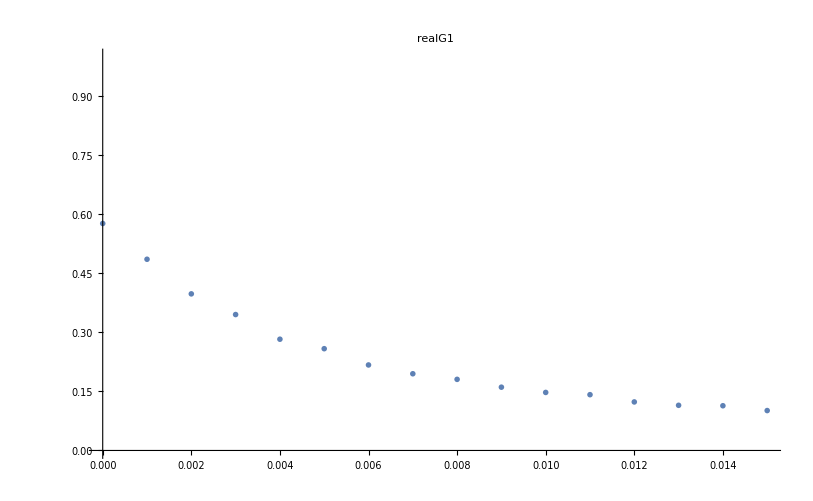

B2 ⅇ^(-d π t)

FittedModel[0.544782 ⅇ^(-137.47 t)]

| Estimate | Standard Error | t-Statistic | P-Value
d | 43.7579 | 2.05002 | 21.3451 | 1.6682×10^-11
B2 | 0.544782 | 0.014833 | 36.7276 | 1.61093×10^-14

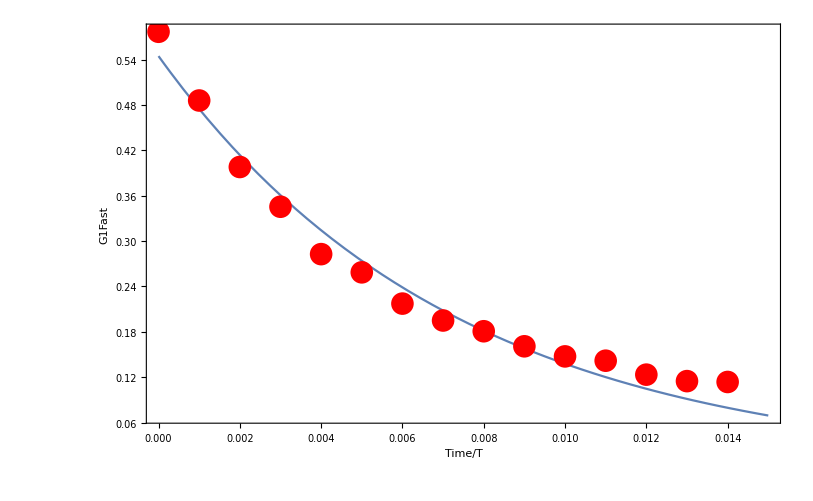

```mathematica
cutOff = 0.015;
ListPlot[realG1,PlotRange->{{0,cutOff},{0,1}}, 
PlotLabel->"realG1",PlotMarkers->{Automatic,Small}]
secondNum=IntegerPart[cutOff/realG1[[2,1]]];
secondExp=Take[realG1,secondNum];
exponentialModel2=B2 Exp[- d Pi t]
fitExp2=NonlinearModelFit[secondExp,{exponentialModel2},{d,B2},{t}]
fitExp2["ParameterTable"]
Show[{Plot[fitExp2[x],{x,0,cutOff},PlotRange->All,BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.02],Map[Point,secondExp]}]},Frame->True,FrameLabel->{"Time/T","G1Fast"}]
```

```mathematica
secondTc = 1/(d Pi)/.fitExp2["BestFitParameters"]
```

0.00727434

```mathematica
Integrate[Exp[-i w t]Exp[-t/tau],{t,0,Infinity}]
```

ConditionalExpression[tau/(1+i tau w),Re[1/tau+i w]>0]

```mathematica
Mean[intensity]
```

3.83459

```mathematica
1/160.
```

0.00625

```mathematica
Sqrt[10.]
```

3.16228